## Setup

#### Docked cell

```mathematica
CurrentValue[EvaluationNotebook[],DockedCells]={};
```

```mathematica
ResourceFunction["https://www.wolframcloud.com/obj/nikm/DeveloperDockedCell"]["Wolfram`Cotengra`",
FileNameJoin[{NotebookDirectory[],"..","Cotengra"}]]
```

## Playground

```mathematica
PacletInstall["https://www.wolframcloud.com/obj/wolframquantumframework/Cotengra.paclet",ForceVersionInstall->True]
```

PacletObject[…]

```mathematica
<<Wolfram`Cotengra`
```

```mathematica
?Wolfram`Cotengra`*
```

```mathematica
<<Wolfram`QuantumFramework`
```

```mathematica
qc=;
```

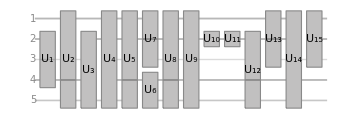

```mathematica
qc["Diagram"]
```

```mathematica
net=qc["TensorNetwork"];
tnData=TensorNetworkData@net;
```

```mathematica
Cases[tnData["Contractions"],tag:{_[v_,_],_[w_,_]}:>DirectedEdge[v,w,tag],{-3}]
```

{-42{(-4)^1,2_1},-31{(-3)^2,1_2},-22{(-2)^3,2_3},-11{(-1)^4,1_4},02{0^5,2_5},13{1^4,3_4},-31{(-3)^2,1_2},-11{(-1)^4,1_4},24{2^1,4_1},23{2^3,3_3},23{2^5,3_5},-42{(-4)^1,2_1},-22{(-2)^3,2_3},02{0^5,2_5},34{3^2,4_2},34{3^5,4_5},23{2^3,3_3},13{1^4,3_4},23{2^5,3_5},45{4^1,5_1},45{4^2,5_2},45{4^3,5_3},46{4^4,6_4},45{4^5,5_5},24{2^1,4_1},34{3^2,4_2},34{3^5,4_5},57{5^1,7_1},58{5^2,8_2},45{4^1,5_1},45{4^2,5_2},45{4^3,5_3},45{4^5,5_5},69{6^4,9_4},68{6^5,8_5},46{4^4,6_4},78{7^3,8_3},57{5^1,7_1},89{8^1,9_1},89{8^2,9_2},89{8^3,9_3},89{8^5,9_5},58{5^2,8_2},78{7^3,8_3},68{6^5,8_5},913{9^1,13_1},910{9^2,10_2},912{9^3,12_3},914{9^4,14_4},912{9^5,12_5},89{8^1,9_1},89{8^2,9_2},89{8^3,9_3},69{6^4,9_4},89{8^5,9_5},1011{10^2,11_2},910{9^2,10_2},1112{11^2,12_2},1011{10^2,11_2},1214{12^2,14_2},1214{12^5,14_5},1112{11^2,12_2},912{9^3,12_3},912{9^5,12_5},1314{13^1,14_1},1314{13^3,14_3},913{9^1,13_1},1415{14^3,15_3},1314{13^1,14_1},1214{12^2,14_2},1314{13^3,14_3},914{9^4,14_4},1214{12^5,14_5},1415{14^3,15_3}}

```mathematica
Map[First,tnData["Contractions"],{-3}]
```

{{(-4)^1},{(-3)^2},{(-2)^3},{(-1)^4},{0^5},{1^4,(-3)^2,(-1)^4},{2^1,2^3,2^5,(-4)^1,(-2)^3,0^5},{3^2,3^5,2^3,1^4,2^5},{4^1,4^2,4^3,4^4,4^5,2^1,3^2,3^5},{5^1,5^2,4^1,4^2,4^3,4^5},{6^4,6^5,4^4},{7^3,5^1},{8^1,8^2,8^3,8^5,5^2,7^3,6^5},{9^1,9^2,9^3,9^4,9^5,8^1,8^2,8^3,6^4,8^5},{10^2,9^2},{11^2,10^2},{12^2,12^5,11^2,9^3,9^5},{13^1,13^3,9^1},{14^3,14^4,14^5,13^1,12^2,13^3,9^4,12^5},{15^1,15^2,15^3,14^3}}

```mathematica
tnData["ContractionIndices"]
```

{{(-4)^1},{(-3)^2},{(-2)^3},{(-1)^4},{0^5},{1^4,(-3)^2,(-1)^4},{2^1,2^3,2^5,(-4)^1,(-2)^3,0^5},{3^2,3^5,2^3,1^4,2^5},{4^1,4^2,4^3,4^4,4^5,2^1,3^2,3^5},{5^1,5^2,4^1,4^2,4^3,4^5},{6^4,6^5,4^4},{7^3,5^1},{8^1,8^2,8^3,8^5,5^2,7^3,6^5},{9^1,9^2,9^3,9^4,9^5,8^1,8^2,8^3,6^4,8^5},{10^2,9^2},{11^2,10^2},{12^2,12^5,11^2,9^3,9^5},{13^1,13^3,9^1},{14^3,14^4,14^5,13^1,12^2,13^3,9^4,12^5},{15^1,15^2,15^3,14^3}}

```mathematica
tnData
```

<|Tensors→{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[<18432>, {4, 4, 2, 4, 3, 4, 4, 3}],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[<147456>, {4, 4, 2, 4, 3, 4, 4, 2, 4, 3}],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]},Dimensions→{{4},{4},{2},{4},{3},{4,4,4},{4,2,3,4,2,3},{4,3,2,4,3},{4,4,2,4,3,4,4,3},{4,4,4,4,2,3},{4,3,4},{2,4},{4,4,2,3,4,2,3},{4,4,2,4,3,4,4,2,4,3},{4,4},{4,4},{4,3,4,2,3},{4,2,4},{2,4,3,4,4,2,4,3},{4,4,2,2}},Indices→{{(-4)^1},{(-3)^2},{(-2)^3},{(-1)^4},{0^5},{1^4,1_2,1_4},{2^1,2^3,2^5,2_1,2_3,2_5},{3^2,3^5,3_3,3_4,3_5},{4^1,4^2,4^3,4^4,4^5,4_1,4_2,4_5},{5^1,5^2,5_1,5_2,5_3,5_5},{6^4,6^5,6_4},{7^3,7_1},{8^1,8^2,8^3,8^5,8_2,8_3,8_5},{9^1,9^2,9^3,9^4,9^5,9_1,9_2,9_3,9_4,9_5},{10^2,10_2},{11^2,11_2},{12^2,12^5,12_2,12_3,12_5},{13^1,13^3,13_1},{14^3,14^4,14^5,14_1,14_2,14_3,14_4,14_5},{15^1,15^2,15^3,15_3}},Vertices→{-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},FreeIndices→{15^1,15^2,15^3,14^4,14^5},Bonds→{-3→{1,4},-1→{1,4},-4→{2,4},-2→{2,2},0→{2,3},2→{3,2},1→{3,4},2→{3,3},2→{4,4},3→{4,4},3→{4,3},4→{5,4},4→{5,4},4→{5,2},4→{5,3},4→{6,4},5→{7,4},5→{8,4},7→{8,2},6→{8,3},8→{9,4},8→{9,4},8→{9,2},6→{9,4},8→{9,3},9→{10,4},10→{11,4},11→{12,4},9→{12,2},9→{12,3},9→{13,4},13→{14,4},12→{14,4},13→{14,2},9→{14,4},12→{14,3},14→{15,2}},Contractions→{{{(-4)^1,2_1}},{{(-3)^2,1_2}},{{(-2)^3,2_3}},{{(-1)^4,1_4}},{{0^5,2_5}},{{1^4,3_4},{(-3)^2,1_2},{(-1)^4,1_4}},{{2^1,4_1},{2^3,3_3},{2^5,3_5},{(-4)^1,2_1},{(-2)^3,2_3},{0^5,2_5}},{{3^2,4_2},{3^5,4_5},{2^3,3_3},{1^4,3_4},{2^5,3_5}},{{4^1,5_1},{4^2,5_2},{4^3,5_3},{4^4,6_4},{4^5,5_5},{2^1,4_1},{3^2,4_2},{3^5,4_5}},{{5^1,7_1},{5^2,8_2},{4^1,5_1},{4^2,5_2},{4^3,5_3},{4^5,5_5}},{{6^4,9_4},{6^5,8_5},{4^4,6_4}},{{7^3,8_3},{5^1,7_1}},{{8^1,9_1},{8^2,9_2},{8^3,9_3},{8^5,9_5},{5^2,8_2},{7^3,8_3},{6^5,8_5}},{{9^1,13_1},{9^2,10_2},{9^3,12_3},{9^4,14_4},{9^5,12_5},{8^1,9_1},{8^2,9_2},{8^3,9_3},{6^4,9_4},{8^5,9_5}},{{10^2,11_2},{9^2,10_2}},{{11^2,12_2},{10^2,11_2}},{{12^2,14_2},{12^5,14_5},{11^2,12_2},{9^3,12_3},{9^5,12_5}},{{13^1,14_1},{13^3,14_3},{9^1,13_1}},{{14^3,15_3},14^4,14^5,{13^1,14_1},{12^2,14_2},{13^3,14_3},{9^4,14_4},{12^5,14_5}},{15^1,15^2,15^3,{14^3,15_3}}},ContractionIndices→{{(-4)^1},{(-3)^2},{(-2)^3},{(-1)^4},{0^5},{1^4,(-3)^2,(-1)^4},{2^1,2^3,2^5,(-4)^1,(-2)^3,0^5},{3^2,3^5,2^3,1^4,2^5},{4^1,4^2,4^3,4^4,4^5,2^1,3^2,3^5},{5^1,5^2,4^1,4^2,4^3,4^5},{6^4,6^5,4^4},{7^3,5^1},{8^1,8^2,8^3,8^5,5^2,7^3,6^5},{9^1,9^2,9^3,9^4,9^5,8^1,8^2,8^3,6^4,8^5},{10^2,9^2},{11^2,10^2},{12^2,12^5,11^2,9^3,9^5},{13^1,13^3,9^1},{14^3,14^4,14^5,13^1,12^2,13^3,9^4,12^5},{15^1,15^2,15^3,14^3}}|>

```mathematica
tnData["Contractions"]
```

{{{(-4)^1,2_1}},{{(-3)^2,1_2}},{{(-2)^3,2_3}},{{(-1)^4,1_4}},{{0^5,2_5}},{{1^4,3_4},{(-3)^2,1_2},{(-1)^4,1_4}},{{2^1,4_1},{2^3,3_3},{2^5,3_5},{(-4)^1,2_1},{(-2)^3,2_3},{0^5,2_5}},{{3^2,4_2},{3^5,4_5},{2^3,3_3},{1^4,3_4},{2^5,3_5}},{{4^1,5_1},{4^2,5_2},{4^3,5_3},{4^4,6_4},{4^5,5_5},{2^1,4_1},{3^2,4_2},{3^5,4_5}},{{5^1,7_1},{5^2,8_2},{4^1,5_1},{4^2,5_2},{4^3,5_3},{4^5,5_5}},{{6^4,9_4},{6^5,8_5},{4^4,6_4}},{{7^3,8_3},{5^1,7_1}},{{8^1,9_1},{8^2,9_2},{8^3,9_3},{8^5,9_5},{5^2,8_2},{7^3,8_3},{6^5,8_5}},{{9^1,13_1},{9^2,10_2},{9^3,12_3},{9^4,14_4},{9^5,12_5},{8^1,9_1},{8^2,9_2},{8^3,9_3},{6^4,9_4},{8^5,9_5}},{{10^2,11_2},{9^2,10_2}},{{11^2,12_2},{10^2,11_2}},{{12^2,14_2},{12^5,14_5},{11^2,12_2},{9^3,12_3},{9^5,12_5}},{{13^1,14_1},{13^3,14_3},{9^1,13_1}},{{14^3,15_3},14^4,14^5,{13^1,14_1},{12^2,14_2},{13^3,14_3},{9^4,14_4},{12^5,14_5}},{15^1,15^2,15^3,{14^3,15_3}}}

```mathematica
tnData["Contractions"]
```

{{{(-4)^1,2_1}},{{(-3)^2,1_2}},{{(-2)^3,2_3}},{{(-1)^4,1_4}},{{0^5,2_5}},{{1^4,3_4},{(-3)^2,1_2},{(-1)^4,1_4}},{{2^1,4_1},{2^3,3_3},{2^5,3_5},{(-4)^1,2_1},{(-2)^3,2_3},{0^5,2_5}},{{3^2,4_2},{3^5,4_5},{2^3,3_3},{1^4,3_4},{2^5,3_5}},{{4^1,5_1},{4^2,5_2},{4^3,5_3},{4^4,6_4},{4^5,5_5},{2^1,4_1},{3^2,4_2},{3^5,4_5}},{{5^1,7_1},{5^2,8_2},{4^1,5_1},{4^2,5_2},{4^3,5_3},{4^5,5_5}},{{6^4,9_4},{6^5,8_5},{4^4,6_4}},{{7^3,8_3},{5^1,7_1}},{{8^1,9_1},{8^2,9_2},{8^3,9_3},{8^5,9_5},{5^2,8_2},{7^3,8_3},{6^5,8_5}},{{9^1,13_1},{9^2,10_2},{9^3,12_3},{9^4,14_4},{9^5,12_5},{8^1,9_1},{8^2,9_2},{8^3,9_3},{6^4,9_4},{8^5,9_5}},{{10^2,11_2},{9^2,10_2}},{{11^2,12_2},{10^2,11_2}},{{12^2,14_2},{12^5,14_5},{11^2,12_2},{9^3,12_3},{9^5,12_5}},{{13^1,14_1},{13^3,14_3},{9^1,13_1}},{{14^3,15_3},14^4,14^5,{13^1,14_1},{12^2,14_2},{13^3,14_3},{9^4,14_4},{12^5,14_5}},{15^1,15^2,15^3,{14^3,15_3}}}

```mathematica
MapThread[Annotation[#1,"Tensor"->#2,"Index"->Map[First,#3]]&,{tnData["Vertices"],tnData["Tensors"],tnData["Contractions"]}]
```

{-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

```mathematica
Cases[tnData["Contractions"],{i:_[v_,_],j:_[w_,_]}:>DirectedEdge[v,w,{i,j}],{-3}]
```

{-42{(-4)^1,2_1},-31{(-3)^2,1_2},-22{(-2)^3,2_3},-11{(-1)^4,1_4},02{0^5,2_5},13{1^4,3_4},-31{(-3)^2,1_2},-11{(-1)^4,1_4},24{2^1,4_1},23{2^3,3_3},23{2^5,3_5},-42{(-4)^1,2_1},-22{(-2)^3,2_3},02{0^5,2_5},34{3^2,4_2},34{3^5,4_5},23{2^3,3_3},13{1^4,3_4},23{2^5,3_5},45{4^1,5_1},45{4^2,5_2},45{4^3,5_3},46{4^4,6_4},45{4^5,5_5},24{2^1,4_1},34{3^2,4_2},34{3^5,4_5},57{5^1,7_1},58{5^2,8_2},45{4^1,5_1},45{4^2,5_2},45{4^3,5_3},45{4^5,5_5},69{6^4,9_4},68{6^5,8_5},46{4^4,6_4},78{7^3,8_3},57{5^1,7_1},89{8^1,9_1},89{8^2,9_2},89{8^3,9_3},89{8^5,9_5},58{5^2,8_2},78{7^3,8_3},68{6^5,8_5},913{9^1,13_1},910{9^2,10_2},912{9^3,12_3},914{9^4,14_4},912{9^5,12_5},89{8^1,9_1},89{8^2,9_2},89{8^3,9_3},69{6^4,9_4},89{8^5,9_5},1011{10^2,11_2},910{9^2,10_2},1112{11^2,12_2},1011{10^2,11_2},1214{12^2,14_2},1214{12^5,14_5},1112{11^2,12_2},912{9^3,12_3},912{9^5,12_5},1314{13^1,14_1},1314{13^3,14_3},913{9^1,13_1},1415{14^3,15_3},1314{13^1,14_1},1214{12^2,14_2},1314{13^3,14_3},914{9^4,14_4},1214{12^5,14_5},1415{14^3,15_3}}

```mathematica
tnData["Contractions"]
```

{{{(-4)^1,2_1}},{{(-3)^2,1_2}},{{(-2)^3,2_3}},{{(-1)^4,1_4}},{{0^5,2_5}},{{1^4,3_4},{(-3)^2,1_2},{(-1)^4,1_4}},{{2^1,4_1},{2^3,3_3},{2^5,3_5},{(-4)^1,2_1},{(-2)^3,2_3},{0^5,2_5}},{{3^2,4_2},{3^5,4_5},{2^3,3_3},{1^4,3_4},{2^5,3_5}},{{4^1,5_1},{4^2,5_2},{4^3,5_3},{4^4,6_4},{4^5,5_5},{2^1,4_1},{3^2,4_2},{3^5,4_5}},{{5^1,7_1},{5^2,8_2},{4^1,5_1},{4^2,5_2},{4^3,5_3},{4^5,5_5}},{{6^4,9_4},{6^5,8_5},{4^4,6_4}},{{7^3,8_3},{5^1,7_1}},{{8^1,9_1},{8^2,9_2},{8^3,9_3},{8^5,9_5},{5^2,8_2},{7^3,8_3},{6^5,8_5}},{{9^1,13_1},{9^2,10_2},{9^3,12_3},{9^4,14_4},{9^5,12_5},{8^1,9_1},{8^2,9_2},{8^3,9_3},{6^4,9_4},{8^5,9_5}},{{10^2,11_2},{9^2,10_2}},{{11^2,12_2},{10^2,11_2}},{{12^2,14_2},{12^5,14_5},{11^2,12_2},{9^3,12_3},{9^5,12_5}},{{13^1,14_1},{13^3,14_3},{9^1,13_1}},{{14^3,15_3},14^4,14^5,{13^1,14_1},{12^2,14_2},{13^3,14_3},{9^4,14_4},{12^5,14_5}},{15^1,15^2,15^3,{14^3,15_3}}}

```mathematica
reconstructNet=Graph[
MapThread[Annotation[#1,"Tensor"->#2,"Index"->Replace[#3,pair_List:>FirstCase[pair,_[#1,_]],1]]&,{tnData["Vertices"],tnData["Tensors"],tnData["Contractions"]}],
Cases[tnData["Contractions"],{i:_[v_,_],j:_[w_,_]}:>DirectedEdge[v,w,{i,j}],{-3}]
]
```

-Graphics-

```mathematica
ContractTensorNetwork[reconstructNet]
```

SparseArray[…]

```mathematica
t1=ActivateTensor@EinsteinSummation[tnData["ContractionIndices"],tnData["Tensors"]];
```

```mathematica
{input,output,dimensions}=TensorNetworkContractionPath[net,"ReturnParameters"->True]
```

{{{3},{1},{4},{2},{5},{7,1,2},{9,6,8,3,4,5},{10,11,6,7,8},{12,13,14,16,15,9,10,11},{17,18,12,13,14,15},{24,20,16},{19,17},{21,22,23,25,18,19,20},{31,26,29,35,30,21,22,23,24,25},{27,26},{28,27},{33,36,28,29,30},{32,34,31},{37,38,39,32,33,34,35,36},{40,41,42,37}},{40,41,42,38,39},<|3→4,1→4,4→2,2→4,5→3,7→4,9→4,6→2,8→3,10→4,11→3,12→4,13→4,14→2,16→4,15→3,17→4,18→4,24→4,20→3,19→2,21→4,22→4,23→2,25→3,31→4,26→4,29→2,35→4,30→3,27→4,28→4,33→4,36→3,32→4,34→2,37→2,38→4,39→3,40→4,41→4,42→2|>}

```mathematica
path0=GreedyPath[input,output,dimensions]
```

{{13,14},{11,19},{9,10},{13,14},{9,15},{1,7},{4,14},{3,4},{2,11},{2,11},{8,10},{6,9},{2,3},{1,5},{4,6},{4,5},{1,4},{2,3},{1,2}}

```mathematica
path1=OptimalPath[input,output,dimensions,"limit"]
```

{{15,16},{15,19},{1,7},{4,17},{2,16},{1,3},{1,14},{1,13},{11,12},{1,11},{1,10},{2,9},{1,8},{1,7},{1,6},{4,5},{1,4},{1,3},{1,2}}

```mathematica
path2=OptimalPath[input,output,dimensions,"size"]
```

{{1,7},{2,19},{1,4},{1,17},{2,16},{14,15},{1,14},{1,13},{1,12},{1,11},{1,10},{1,9},{1,8},{1,7},{1,6},{1,5},{1,4},{1,3},{1,2}}

```mathematica
TensorNetworkContractPath[net,path0];//ResourceFunction["TimeMemoryUsed"]
```

{0.046409,35604064,Null}

```mathematica
TensorNetworkContractPath[net,path1];//ResourceFunction["TimeMemoryUsed"]
```

{0.022027,30731248,Null}

```mathematica
TensorNetworkContractPath[net,path2];//ResourceFunction["TimeMemoryUsed"]
```

{0.020987,30716384,Null}

Grouped contraction indices following the path order:

```mathematica
PathIndexContractions[CanonicalPath[path],tnData["Contractions"]]
```

{{{13^1,14_1},{13^3,14_3}},{{5^1,7_1}},{{6^5,8_5}},{{9^3,12_3},{9^5,12_5}},{{10^2,11_2}},{{9^2,10_2},{11^2,12_2}},{{6^4,9_4},{8^1,9_1},{8^2,9_2},{8^3,9_3},{8^5,9_5}},{{(-1)^4,1_4}},{{1^4,3_4}},{{(-3)^2,1_2},{5^2,8_2},{7^3,8_3}},{{3^2,4_2},{3^5,4_5},{4^1,5_1},{4^2,5_2},{4^3,5_3},{4^4,6_4},{4^5,5_5}},{{2^1,4_1},{2^3,3_3},{2^5,3_5}},{{0^5,2_5}},{{(-4)^1,2_1},{9^1,13_1},{9^4,14_4},{12^2,14_2},{12^5,14_5},{14^3,15_3}},{{(-2)^3,2_3}}}

Grouped global contraction indices:

```mathematica
PathIndexContractions[CanonicalPath[path],tnData["Indices"],tnData["Contractions"]]
```

{{{65,71},{66,73}},{{28,38}},{{35,45}},{{48,63},{50,64}},{{56,59}},{{47,57},{58,62}},{{34,54},{39,51},{40,52},{41,53},{42,55}},{{4,8}},{{6,18}},{{2,7},{29,43},{37,44}},{{15,26},{16,27},{20,30},{21,31},{22,32},{23,36},{24,33}},{{9,25},{10,17},{11,19}},{{5,14}},{{1,12},{46,67},{49,74},{60,72},{61,75},{68,79}},{{3,13}}}

Flat list of contraction index pairs for TensorContract:

```mathematica
pathContraction=PathIndexContractions[CanonicalPath[path1],tnData]
```

{{56,59},{58,62},{1,12},{5,14},{3,13},{2,7},{4,8},{6,18},{10,17},{11,19},{9,25},{15,26},{16,27},{20,30},{21,31},{22,32},{24,33},{28,38},{23,36},{29,43},{35,45},{37,44},{34,54},{39,51},{40,52},{41,53},{42,55},{47,57},{48,63},{50,64},{46,67},{49,74},{60,72},{61,75},{65,71},{66,73},{68,79}}

```mathematica
t2=First@TensorContract[Inactive[TensorProduct]@@tnData["Tensors"],pathContraction]
```

SparseArray[…]

```mathematica
Chop[t1-t2,1*^-7]
```

SparseArray[…]

```mathematica
PathToTreePath[path]
```

{{20},{{19},{{18},{{{17},{{15},{16}}},{{14},{{13},{{11},{{12},{{10},{{9},{{{3},{{5},{{1},{7}}}},{{8},{{4},{{2},{6}}}}}}}}}}}}}}}

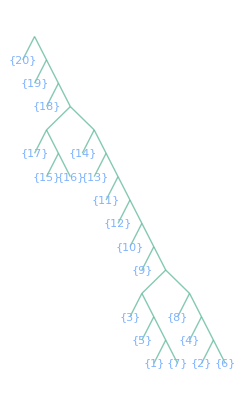

```mathematica
Map[Tree[Null,#]&,PathToTreePath[path],{0,-3}]
```